# Phase portrait, vector field plotting

## Harmonic oscillator (∂_(t,t) x + x = 0)

```mathematica
Clear[tmax,Tm]
t0=0.0;
tmax=6.23;
x0=1.0;(*initial position*)
y0=0.0;(*initial velocity (speed)*)
x02=0.5;(*initial position, second solution*)
y02=0.0;(*initial velocity (speed), second solution*)
Manipulate[
sol=NDSolve[{
x'[t]==y[t],
y'[t]==-x[t],
x[0]==x0,y[0]==y0},
{x,y},{t,t0,Tm}];
sol2=NDSolve[{
x'[t]==y[t],
y'[t]==-x[t],
x[0]==x02,y[0]==y02},
{x,y},{t,t0,Tm}];
l={x[t],y[t]};
ParPlot=ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],Evaluate[{x[t],y[t]}/.sol2]},{t,t0,Tm},PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotPoints->1000,AxesLabel->TraditionalForm/@l,ImageSize->Medium,LabelStyle->20];
xplot=Plot[{Evaluate[x[t]/.sol],Evaluate[x[t]/.sol2]},{t,t0,Tm},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->Medium,LabelStyle->20];
yplot=Plot[{Evaluate[y[t]/.sol],Evaluate[y[t]/.sol2]},{t,t0,Tm},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->Medium,LabelStyle->20];
Grid[{{ParPlot,yplot},{xplot}},Frame->All],
{{Tm,0.5 tmax,"Integration time, t"},1,tmax,Appearance->"Labeled"}, SaveDefinitions->True,TrackedSymbols:>{Tm}]
```

## Phase portrait, visualisation styles (harmonic oscillator (∂_(t,t) x + x = 0))

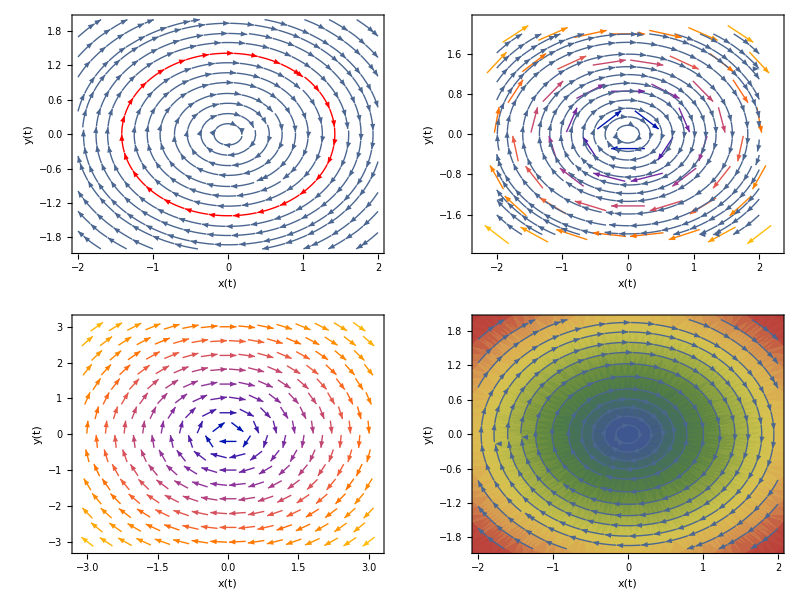

```mathematica
Grid[{
{StreamPlot[{y,-x},{x,-2,2},{y,-2,2},FrameLabel->{x[t],y[t]}, StreamPoints->{{{{1,1},Red},Automatic}},ImageSize->370,LabelStyle->20],
StreamPlot[{y,-x},{x,-2,2},{y,-2,2},VectorPoints->8,VectorStyle->Red,FrameLabel->{x[t],y[t]},ImageSize->370,LabelStyle->20]},
{VectorPlot[{y,-x},{x,-3,3},{y,-3,3},FrameLabel->{x[t],y[t]},ImageSize->370,LabelStyle->20],StreamDensityPlot[{y,-x},{x,-2,2},{y,-2,2},ColorFunction->"DarkRainbow",FrameLabel->{x[t],y[t]},ImageSize->370,LabelStyle->20]}},Frame->All]
```

## Relationship between phase portrait and integrated time domain solutions

### Damped harmonic oscillator (∂_(t,t) x - ∂_t x + x = 0)

```mathematica
imagesize=360;
xdom=1;ydom=1;maxT=20;

diffX=y[t];
diffY=-y[t]-3 x[t];
splot=StreamPlot[{y,-y-3 x},{x,-xdom,xdom},{y,-ydom,ydom},FrameLabel->{x[t],y[t]},ImageSize->imagesize,LabelStyle->15];
fixedp=Graphics[{PointSize[0.024],Blue,Point[{0,0}]}];

Manipulate[
integration=NDSolve[{
x'[t]==diffX,
y'[t]==diffY,
x[0]==point[[1]],y[0]==point[[2]]},
{x,y},{t,0,T}];
trajectory=ParametricPlot[
Evaluate[{x[t],y[t]}/.integration],
{t,0,T},PlotStyle->Red];
solx=Plot[
Evaluate[x[t]/.integration],
{t,0,T},PlotRange-> All,AxesLabel-> {t,x[t]},ImageSize->imagesize,LabelStyle->15];
soly=Plot[
Evaluate[y[t]/.integration],
{t,0,T},PlotRange-> All,AxesLabel-> {t,y[t]},ImageSize->imagesize,LabelStyle->15];
Grid[{{Show[splot,trajectory,fixedp],soly},{solx}},Frame->All],
{{T,0.45 maxT,"Integration time, t"},1,maxT,Appearance->"Labeled"},{{point,{0.5 xdom,0.5 ydom}},Locator}, SaveDefinitions->True, TrackedSymbols:>{T,point}]
```

Creation of this notebook was supported by IT Academy program of Information Technology Foundation for Education (HITSA).